(R v (249.15+((2 √(g hc IC m)+g L0 m t1) V)/(Lp π r^2 R t1 v)))/V

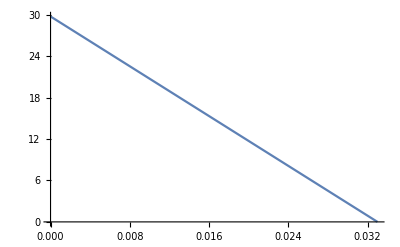

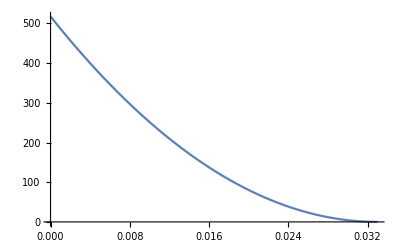

```mathematica
T=(V*(m*g*L0*t1+2*Sqrt[m*g*IC*hc]))/(Pi*(r)^2*Lp*v*R*t1)+249.15;
Tmax=305.106;
dP= (T-249.15)*v*R/V;
P=(T*v*R)/V
{m,g,ρ,hc,L0,Lp,v,R,r,V,t1,t2,IC}={0.006,9.8,1.17,0.000688,0.0125,0.0135,0.0175,8.3138,0.00875,0.00033,0.0195,0.033,21.02*10^(-7)};
a=dP/((t2)^2);
b=-2*t2*a;
c=hc/t2;
h[t]=c*t;
Vspeed[t]=Sqrt[(2*(a*(t^2)+b*t+dP))/ρ];
Plot[Vspeed[t],{t,0,t2}]
Plot[a*(t^2)+b*t+dP,{t,0,t2}]
Plot[c*t,{t,0,t2}]
Vloss=Integrate[Pi*h[t]*((Vspeed[t]*t)^2+2*Vspeed[t]*L0*t),{t,0,t2}];
vloss=Vloss*1000/22.4;
n=(v-(P*V)/(R*Tmax))/(vloss)
```

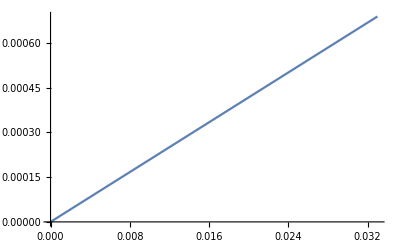

-Graphics-